```mathematica
ClearAll["Global`*"];
```

```mathematica
PES[x_,y_]:=Cos[2 Pi x] (1+5y)+2 Pi y^2+2 Cos[Pi x];
XGrad[x_,y_]:=Derivative[1,0][PES][x,y];
YGrad[x_,y_]:=Derivative[0,1][PES][x,y];
PESGrad[x_,y_]:=XGrad[x,y]+YGrad[x,y];
```

find (and confirm) all the minima, saddle points, and all the minimum-energy pathways connecting the minima. Obtain the energy barrier for each minimum-energy pathway. To obtain maximum credit, please ensure that all quantities are converged
Plot the PES, and additionally make a log contour plot in order to see the minima and saddle points clearly

```mathematica
Plot3D[PES[x,y],{x,-2,2},{y,-1,1},PlotPoints->80,AxesLabel->{"x","y","E(x,y)"},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ContourPlot[Log[PES[x,y]+5],{x,-2,2},{y,-2,2},FrameLabel->{"x","y"},ColorFunction->"Rainbow",Contours->20,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->"E(x,y)"],{After,Top}]]
```

-Graphics-

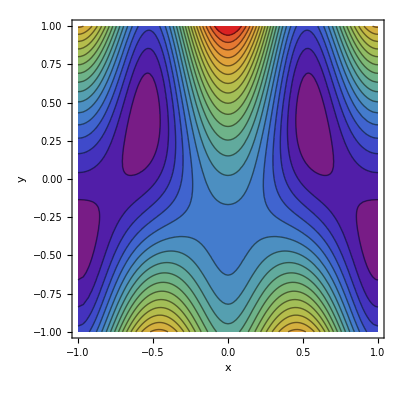

```mathematica
ContourPlot[PES[x,y],{x,-1,1},{y,-1,1},FrameLabel->{"x","y"},ColorFunction->"Rainbow",Contours->20,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->6]&),LegendLabel->"E(x,y)"],{After,Top}]]
```

```mathematica
Hess=({{D[PES[x,y], x,x], D[PES[x,y], x,y]}, {D[PES[x,y], y,x], D[PES[x,y], y,y]}});
MatrixForm[Hess]
```

(-2 π^2 Cos[π x]-4 π^2 (1+5 y) Cos[2 π x] | -10 π Sin[2 π x]
-10 π Sin[2 π x] | 4 π)

Find all the minima and saddlepoints in a period [-1,1]

```mathematica
root11 =FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,-1},{y,0.0}]
root12 =FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,-0.5},{y,0.0}]
root13= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,0},{y,0.0}]
root14= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,0.5},{y,0.0}]
root15= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,1},{y,0.0}]
root21= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,-0.75},{y,0.0}]
root22= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,-0.2},{y,0.0}]
root23= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,0.2},{y,0.0}]
root24= FindRoot[{XGrad[x,y]==0,YGrad[x,y]==0},{x,0.75},{y,0.0}]

coord11=Evaluate[{x11,y11}/.root11];
coord12=Evaluate[{x12,y12}/.root12];coord13=Evaluate[{x13,y13}/.root13];
coord14=Evaluate[{x14,y14}/.root14];
coord15=Evaluate[{x15,y15}/.root15];
coord21=Evaluate[{x21,y21}/.root21];
coord22=Evaluate[{x22,y22}/.root22];
coord23=Evaluate[{x23,y23}/.root23];coord24=Evaluate[{x24,y24}/.root24];
```

{x→-1.,y→-0.397887}

{x→-0.555768,y→0.37371}

{x→0.,y→-0.397887}

{x→0.555768,y→0.37371}

{x→1.,y→-0.397887}

{x→-0.777951,y→-0.0695188}

{x→-0.110171,y→-0.306304}

{x→0.110171,y→-0.306304}

{x→0.777951,y→-0.0695188}

### Confirm minima: Evaluate the Hessian and its Eigenvalue at the Minima

```mathematica
Hess11= Evaluate[Hess/.root11];
Print["The Hessian Matrix at ", root11]
MatrixForm[Hess11]
Print["The Eigenvalues of the Hessian at ", root11]
{e1,e2}=Eigenvalues[Hess11]
```

The Hessian Matrix at {x→-1.,y→-0.397887}

(58.8006 | -3.55976×10^-14
-3.55976×10^-14 | 4 π)

The Eigenvalues of the Hessian at {x→-1.,y→-0.397887}

{58.8006,12.5664}

```mathematica
Hess12= Evaluate[Hess/.root12];
Print["The Hessian Matrix at ", root12]
MatrixForm[Hess12]
Print["The Eigenvalues of the Hessian at ", root12]
{e1,e2}=Eigenvalues[Hess12]
```

The Hessian Matrix at {x→-0.555768,y→0.37371}

(109.805 | -10.7842
-10.7842 | 4 π)

The Eigenvalues of the Hessian at {x→-0.555768,y→0.37371}

{110.987,11.3847}

```mathematica
Hess13= Evaluate[Hess/.root13];
Print["The Hessian Matrix at ", root13]
MatrixForm[Hess13]
Print["The Eigenvalues of the Hessian at ", root13]
{e1,e2}=Eigenvalues[Hess13]
```

The Hessian Matrix at {x→0.,y→-0.397887}

(19.3222 | 0.
0. | 4 π)

The Eigenvalues of the Hessian at {x→0.,y→-0.397887}

{19.3222,12.5664}

```mathematica
Hess14= Evaluate[Hess/.root14];
Print["The Hessian Matrix at ", root14]
MatrixForm[Hess14]
Print["The Eigenvalues of the Hessian at ", root14]
{e1,e2}=Eigenvalues[Hess14]
```

The Hessian Matrix at {x→0.555768,y→0.37371}

(109.805 | 10.7842
10.7842 | 4 π)

The Eigenvalues of the Hessian at {x→0.555768,y→0.37371}

{110.987,11.3847}

```mathematica
Hess15= Evaluate[Hess/.root15];
Print["The Hessian Matrix at ", root15]
MatrixForm[Hess15]
Print["The Eigenvalues of the Hessian at ", root15]
{e1,e2}=Eigenvalues[Hess15]
```

The Hessian Matrix at {x→1.,y→-0.397887}

(58.8006 | 3.55976×10^-14
3.55976×10^-14 | 4 π)

The Eigenvalues of the Hessian at {x→1.,y→-0.397887}

{58.8006,12.5664}

### Evaluate the potential at the minima

```mathematica
x11 = Evaluate[x /.root11];
y11 = Evaluate[y/.root11];
Print["The Potential at ", root11]
Print["V = ", PES[ x11,y11]]
```

The Potential at {x→-1.,y→-0.397887}

V = -1.99472

```mathematica
x12 = Evaluate[x /.root12];
y12 = Evaluate[y/.root12];
Print["The Potential at ", root12]
Print["V = ", PES[ x12,y12]]
```

The Potential at {x→-0.555768,y→0.37371}

V = -2.16535

```mathematica
x13 = Evaluate[x /.root13];
y13 = Evaluate[y/.root13];
Print["The Potential at ", root13]
Print["V = ", PES[ x13,y13]]
```

The Potential at {x→0.,y→-0.397887}

V = 2.00528

```mathematica
x14 = Evaluate[x /.root14];
y14 = Evaluate[y/.root14];
Print["The Potential at ", root14]
Print["V = ", PES[ x14,y14]]
```

The Potential at {x→0.555768,y→0.37371}

V = -2.16535

```mathematica
x15 = Evaluate[x /.root15];
y15= Evaluate[y/.root15];
Print["The Potential at ", root15]
Print["V = ", PES[ x15,y15]]
```

The Potential at {x→1.,y→-0.397887}

V = -1.99472

### Confirm saddle points: Evaluate the Hession and its Eigenvalue at the saddle points

```mathematica
Print["The Hessian Matrix at ",root21] 
Hess21=Evaluate[Hess/.root21];
MatrixForm[Hess21]
Print["The Eigenvalues of the Hessian at ",root21]
{e1,e2}=Eigenvalues[Hess21]
```

The Hessian Matrix at {x→-0.777951,y→-0.0695188}

(10.6279 | -30.9327
-30.9327 | 4 π)

The Eigenvalues of the Hessian at {x→-0.777951,y→-0.0695188}

{42.545,-19.3507}

```mathematica
Print["The Hessian Matrix at ",root22] 
Hess22=Evaluate[Hess/.root22];
MatrixForm[Hess22]
Print["The Eigenvalues of the Hessian at ",root22]
{e1,e2}=Eigenvalues[Hess22]
```

The Hessian Matrix at {x→-0.110171,y→-0.306304}

(-2.41494 | 20.0513
20.0513 | 4 π)

The Eigenvalues of the Hessian at {x→-0.110171,y→-0.306304}

{26.4805,-16.3291}

```mathematica
Print["The Hessian Matrix at ",root23] 
Hess23=Evaluate[Hess/.root23];
MatrixForm[Hess23]
Print["The Eigenvalues of the Hessian at ",root23]
{e1,e2}=Eigenvalues[Hess23]
```

The Hessian Matrix at {x→0.110171,y→-0.306304}

(-2.41494 | -20.0513
-20.0513 | 4 π)

The Eigenvalues of the Hessian at {x→0.110171,y→-0.306304}

{26.4805,-16.3291}

```mathematica
Print["The Hessian Matrix at ",root24] 
Hess24=Evaluate[Hess/.root24];
MatrixForm[Hess24]
Print["The Eigenvalues of the Hessian at ",root24]
{e1,e2}=Eigenvalues[Hess24]
```

The Hessian Matrix at {x→0.777951,y→-0.0695188}

(10.6279 | 30.9327
30.9327 | 4 π)

The Eigenvalues of the Hessian at {x→0.777951,y→-0.0695188}

{42.545,-19.3507}

### Evaluate the potential at the saddle points

```mathematica
x21=Evaluate[x/.root21];
 y21=Evaluate[y/.root21];
 Print["The Potential at ",root21]
Print["V = ",PES[x21,y21]]
```

The Potential at {x→-0.777951,y→-0.0695188}

V = -1.38843

```mathematica
x22=Evaluate[x/.root22];
 y22=Evaluate[y/.root22];
 Print["The Potential at ",root22]
Print["V = ",PES[x22,y22]]
```

The Potential at {x→-0.110171,y→-0.306304}

V = 2.06172

```mathematica
x23=Evaluate[x/.root23];
 y23=Evaluate[y/.root23];
 Print["The Potential at ",root23]
Print["V = ",PES[x23,y23]]
```

The Potential at {x→0.110171,y→-0.306304}

V = 2.06172

```mathematica
x24=Evaluate[x/.root24];
 y24=Evaluate[y/.root24];
 Print["The Potential at ",root24]
Print["V = ",PES[x24,y24]]
```

The Potential at {x→0.777951,y→-0.0695188}

V = -1.38843

### Evaluate the barriers

```mathematica
Barrier1=PES[x21,y21]-PES[x11,y11]
```

0.606284

```mathematica
Barrier2=PES[x21,y21]-PES[x12,y12]
```

0.776916

```mathematica
Barrier3=PES[x22,y22]-PES[x12,y12]
```

4.22707

```mathematica
Barrier4=PES[x22,y22]-PES[x13,y13]
```

0.0564387

### Show the critical points on the PES

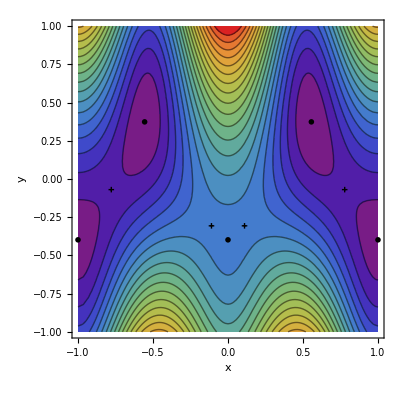

```mathematica
Show[ContourPlot[PES[x,y],{x,-1,1},{y,-1,1},Contours->20,FrameLabel->{"x","y"},ColorFunction->"Rainbow"],ListPlot[{coord11,coord12,coord13,coord14,coord15}, PlotMarkers->{Automatic,Medium},PlotStyle->Black],ListPlot[{coord21,coord22,coord23,coord24}, PlotMarkers->{"+",Large},PlotStyle->Black]]
```

## Find the minimum-energy pathways

```mathematica
Nim =21;
tmax = 100;
ms=200000;
ks =1000.0;
```

```mathematica
{x1,y1}={x15,y15};
{xN,yN}={x13,y13};
```

### eqns

```mathematica
eqns=Join[{x[2]'[t]== -XGrad[x[2][t],y[2][t]]+(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+ ks(√((x[3][t]-x[2][t])^2 +(y[3][t]-y[2][t])^2)-√((x[2][t]-x1)^2 +(y[2][t]-y1)^2))((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))},
{y[2]'[t]== -YGrad[x[2][t],y[2][t]]+(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+ks(√((x[3][t]-x[2][t])^2 +(y[3][t]-y[2][t])^2)-√((x[2][t]-x1)^2 +(y[2][t]-y1)^2))((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))},Table[
x[i]'[t]==-XGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,3,(Nim-2)}],
Table[y[i]'[t]== -YGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,3,(Nim-2)}],{x[(Nim-1)]'[t]== -XGrad[x[Nim-1][t],y[Nim-1][t]]+(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+ks(√((xN-x[(Nim-1)][t])^2 +(yN-y[(Nim-1)][t])^2)-√((x[(Nim-1)][t]-x[(Nim-2)][t])^2 +(y[(Nim-1)][t]-y[(Nim-2)][t])^2))((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))},
{y[(Nim-1)]'[t]== -YGrad[x[Nim-1][t],y[Nim-1][t]]+(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+ks(√((xN-x[(Nim-1)][t])^2 +(yN-y[(Nim-1)][t])^2)-√((x[(Nim-1)][t]-x[(Nim-2)][t])^2 +(y[(Nim-1)][t]-y[(Nim-2)][t])^2))((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))}];
```

### Initial Guess of MEP

```mathematica
Nincx = (xN-x1)/(Nim-1);
Nincy=(yN-y1)/(Nim-1);
eqns= Join[eqns,Table[x[i][0]==x1+Nincx (i-1),{i,2,(Nim-1)}], Table[y[i][0]==y1+Nincy (i-1),{i,2,(Nim-1)}]];
```

### Generate a Table for the Remaining Required Input.

```mathematica
seqns = Join[Table[x[i],{i,2,(Nim-1)}],Table[y[i],{i,2,(Nim-1)}]];
```

### Solve Equations, Store the solution in sol

```mathematica
sol = NDSolve[eqns,seqns,{t,tmax},MaxSteps->ms];
```

### Format MEP in a Suitable Plotting Form

```mathematica
xpath =Flatten[Append[{x1},Flatten[Table[{Evaluate[x[i][tmax]/.sol]},{i,2,(Nim-1)}]]]];
xpath =Flatten[Append[xpath,{xN}]];
ypath=Flatten[Append[{y1},Flatten[Table[{Evaluate[y[i][tmax]/.sol]},{i,2,(Nim-1)}]]]];
ypath =Flatten[Append[ypath,{yN}]];
path = Thread[{xpath,ypath}];
```

## Find the Image with the Maximum Energy and Climb it Up to the Transition State

### First, Find the Index of the Image with the Maximum Energy

```mathematica
Epath=Table[PES[path[[i,1]],path[[i,2]]],{i,1,Nim}];
maxind=Ordering[Epath,-1];
maxind=maxind[[1]];
```

### Now Solve Equations with a Special Equation for the Image with the Maximum Energy; First, Generate Equations

```mathematica
If[maxind ≠2,
{firsteqns=Join[{x[2]'[t]== -XGrad[x[2][t],y[2][t]]+(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+ ks(√((x[3][t]-x[2][t])^2 +(y[3][t]-y[2][t])^2)-√((x[2][t]-x1)^2 +(y[2][t]-y1)^2))((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))},
{y[2]'[t]== -YGrad[x[2][t],y[2][t]]+(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+ks(√((x[3][t]-x[2][t])^2 +(y[3][t]-y[2][t])^2)-√((x[2][t]-x1)^2 +(y[2][t]-y1)^2))((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))}]}];
If[maxind ==2,
{firsteqns=Join[{x[2]'[t]== -XGrad[x[2][t],y[2][t]]+2.0(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))},
{y[2]'[t]== -YGrad[x[2][t],y[2][t]]+2.0(XGrad[x[2][t],y[2][t]] ((x[3][t]-x1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))+YGrad[x[2][t],y[2][t]]((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2))))((y[3][t]-y1)/(√((x[3][t]-x1)^2 +(y[3][t]-y1)^2)))}]}];
If[2<maxind<Nim-1,
{mideqns=Join[
Table[x[i]'[t]==-XGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,3,maxind-1}],
{x[maxind]'[t]==-XGrad[x[maxind][t],y[maxind][t]]+2.0(XGrad[x[maxind][t],y[maxind][t]] ((x[maxind+1][t]-x[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2)))+YGrad[x[maxind][t],y[maxind][t]]((y[maxind+1][t]-y[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2))))((x[maxind+1][t]-x[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2)))},
Table[
x[i]'[t]==-XGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,maxind+1,Nim-2}],
Table[y[i]'[t]== -YGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,3,maxind-1}],

{y[maxind]'[t]== -YGrad[x[maxind][t],y[maxind][t]]+2.0(XGrad[x[maxind][t],y[maxind][t]] ((x[maxind+1][t]-x[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2)))+YGrad[x[maxind][t],y[maxind][t]]((y[maxind+1][t]-y[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2))))((y[maxind+1][t]-y[maxind-1][t])/(√((x[maxind+1][t]-x[maxind-1][t])^2 +(y[maxind+1][t]-y[maxind-1][t])^2)))},

Table[y[i]'[t]== -YGrad[x[i][t],y[i][t]]+(XGrad[x[i][t],y[i][t]] ((x[i+1][t]-x[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+YGrad[x[i][t],y[i][t]]((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2)))+ks(√((x[i+1][t]-x[i][t])^2 +(y[i+1][t]-y[i][t])^2)-√((x[i][t]-x[i-1][t])^2 +(y[i][t]-y[i-1][t])^2))((y[i+1][t]-y[i-1][t])/(√((x[i+1][t]-x[i-1][t])^2 +(y[i+1][t]-y[i-1][t])^2))),{i,maxind+1,Nim-2}]]}];

If[maxind ≠Nim-1,{lasteqns=Join[{x[(Nim-1)]'[t]== -XGrad[x[Nim-1][t],y[Nim-1][t]]+(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+ks(√((xN-x[(Nim-1)][t])^2 +(yN-y[(Nim-1)][t])^2)-√((x[(Nim-1)][t]-x[(Nim-2)][t])^2 +(y[(Nim-1)][t]-y[(Nim-2)][t])^2))((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))},
{y[(Nim-1)]'[t]== -YGrad[x[Nim-1][t],y[Nim-1][t]]+(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+ks(√((xN-x[(Nim-1)][t])^2 +(yN-y[(Nim-1)][t])^2)-√((x[(Nim-1)][t]-x[(Nim-2)][t])^2 +(y[(Nim-1)][t]-y[(Nim-2)][t])^2))((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))}]}];
If[maxind ==Nim-1,{lasteqns=Join[{x[(Nim-1)]'[t]== -XGrad[x[Nim-1][t],y[Nim-1][t]]+2.0(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))},
{y[(Nim-1)]'[t]== -YGrad[x[Nim-1][t],y[Nim-1][t]]+(XGrad[x[Nim-1][t],y[Nim-1][t]]((xN-x[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))+YGrad[x[Nim-1][t],y[Nim-1][t]]((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2))))((yN-y[(Nim-2)][t])/(√((xN-x[(Nim-2)][t])^2 +(yN-y[(Nim-2)][t])^2)))}]}];
eqns= Join[firsteqns,mideqns,lasteqns,Table[x[i][0]==path[[i,1]],{i,2,(Nim-1)}], Table[y[i][0]==path[[i,2]],{i,2,(Nim-1)}]];
seqns = Join[Table[x[i],{i,2,(Nim-1)}],Table[y[i],{i,2,(Nim-1)}]];
```

### Solve the New Equations

```mathematica
sol = NDSolve[eqns,seqns,{t,tmax},MaxSteps->ms];
```

### Format the New Path for Plotting

```mathematica
xpathclimb =Flatten[Append[{x1},Flatten[Table[{Evaluate[x[i][tmax]/.sol]},{i,2,(Nim-1)}]]]];
xpathclimb =Flatten[Append[xpathclimb,{xN}]];
ypathclimb=Flatten[Append[{y1},Flatten[Table[{Evaluate[y[i][tmax]/.sol]},{i,2,(Nim-1)}]]]];
ypathclimb =Flatten[Append[ypathclimb,{yN}]];
Print["Coordinates of MEP with Climbing Image"]
pathclimb = Thread[{xpathclimb,ypathclimb}]
```

Coordinates of MEP with Climbing Image

{{1.,-0.397887},{0.991674,-0.31067},{0.948126,-0.234645},{0.886143,-0.172723},{0.822931,-0.112056},{0.759542,-0.0515747},{0.699372,0.0121103},{0.644039,0.0800403},{0.609087,0.160381},{0.547815,0.223006},{0.601024,0.1534},{0.593734,0.0660895},{0.53746,-0.0010627},{0.471406,-0.0586227},{0.400885,-0.110613},{0.328913,-0.160576},{0.255845,-0.208921},{0.182795,-0.257294},{0.110171,-0.306304},{0.0511259,-0.347332},{0.,-0.397887}}

### Get the Energy and Coordinates of the Transition State from CI-NB and Regular NEB

```mathematica
Epathclimb=Table[PES[pathclimb[[i,1]],pathclimb[[i,2]]],{i,1,Nim}];
maxind=Ordering[Epath,-1];
maxind=maxind[[1]];
xts=pathclimb[[maxind,1]];
yts=pathclimb[[maxind,2]];
tspoint=Thread[{xts,yts}];
Ets=PES[pathclimb[[maxind,1]],pathclimb[[maxind,2]]];
Print["Climbing Image Transition State:  xts = ",xts,"  yts = ",yts,"  Ets = ",Ets]
```

Climbing Image Transition State:  xts = 0.110171  yts = -0.306304  Ets = 2.06172

```mathematica
xt=path[[maxind,1]];
yt=path[[maxind,2]];
Et=PES[path[[maxind,1]],path[[maxind,2]]];
NEBtspoint=Thread[{xt,yt}];
Print["NEB Transition State:  xts = ",xt,"  yts = ",yt,"  Ets = ",Et]
```

NEB Transition State:  xts = 0.127471  yts = -0.294181  Ets = 2.05775

### Plot the PES and MEP

```mathematica
Show[
ListPlot[{path}, PlotMarkers->{Automatic,Small},PlotStyle->Black,Joined->True,PlotStyle->Thick]]
```

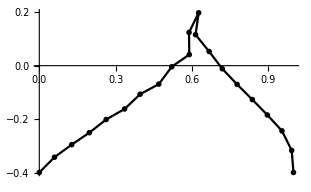
```mathematica
p35=-Graphics-;
```

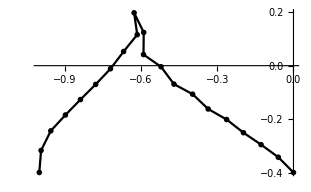
```mathematica
p13=-Graphics-;
```

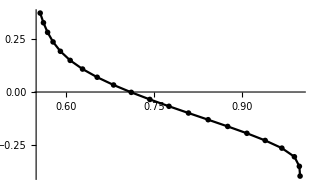
```mathematica
p45=-Graphics-;
```

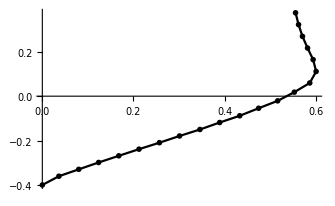
```mathematica
p34=-Graphics-;
```

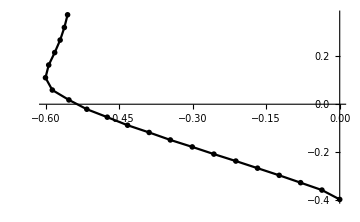
```mathematica
p23=-Graphics-;
```

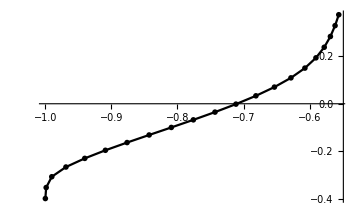
```mathematica
p12=-Graphics-;
```

```mathematica
Show[ContourPlot[PES[x,y],{x,-1.5,1.5},{y,-1,1},Contours->50 ,FrameLabel->{"x","y"},LabelStyle->{FontSize->18,FontFamily->"Arial"},FrameStyle->Thick,ColorFunction->"Rainbow"],
p12,p23,p34,p45,p13,p35,AspectRatio->Automatic]
```

-Graphics-